```mathematica
selectGraphAs["DST"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[2]]&];
gkeys=Map[#[[1,2]]&,gth];
(*as=Inner[Rule,gkeys,gth,Association];*);
as=Association[MapThread[Rule,{gkeys,gth}]];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]//Graph
]
```

```mathematica
selectGraphAs["SRC"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[1]]&];
gkeys=Map[#[[1,1]]&,gth];
(*as=Inner[Rule,gkeys,gth,Association]*);
as=Association[MapThread[Rule,{gkeys,gth}]];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]//Graph
]
```

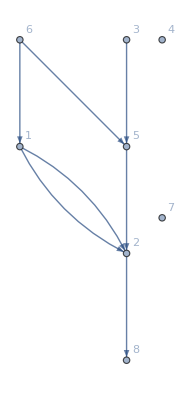

```mathematica
g=Graph[{1,2,3,4,5,6,7,8},{1->2,1->2,3->5,6->5,2->8,5->2,6->1},VertexLabels->Automatic]
```

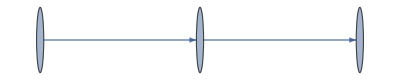

```mathematica
g1=selectGraphAs["SRC"][g,{2,5}]
```

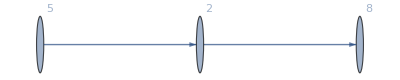

```mathematica
Graph[g1,VertexLabels->Automatic]
```

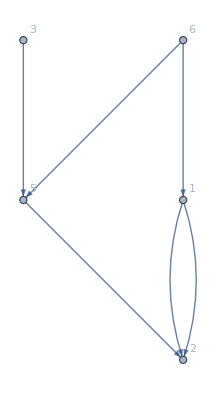

```mathematica
Subgraph[g,{DirectedEdge[_,5],DirectedEdge[_,2]}]
```

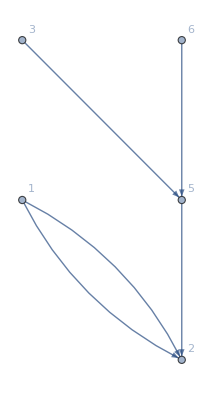

```mathematica
g2=Graph[selectGraphAs["DST"][g,{2,5}],VertexLabels->Automatic]
```

```mathematica
rg=RandomGraph[{50000,100000}]
```

```mathematica
(rv=RandomChoice[rg//VertexList,6000]//Union)//Length
```

5642

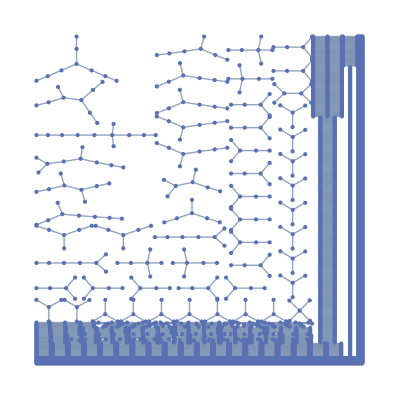

```mathematica
Subgraph[rg,rv]
```